{6.00887,6.00887,6.00887,6.00887,6.00887,6.00887,6.00959,6.00647,6.00647,6.00647,6.00647,6.00647,6.00647,6.00647,6.00647,6.00647,6.00647,6.00647,6.00004,6.00004,5.99345,5.99345,5.99345,5.99345,5.99345,5.99345,5.99345,5.99345,5.99345,5.99345,5.98948,5.98948,5.97836,5.97836,5.97836,5.97836,5.97286,5.97286,5.97286,5.97286,5.97286,5.97286,5.97286,5.96041,5.96041,5.96041,5.96041,5.94572,5.94572,5.94572,5.94572,5.94572,5.94572,5.91431,5.91431,5.91431,5.91431,5.91431,5.91431,5.91431,5.91422,5.91422,5.91422,5.91422,5.90375,5.90375,5.90375,5.90375,5.87979,5.87979,5.87979,5.87979,5.87979,5.87979,5.87979,5.85603,5.85603,5.85603,5.85603,5.85603,5.86227,5.86227,5.86227,5.86227,5.86227,5.80383,5.80383,5.80383,5.80383,5.80383,5.80383,5.79249,5.79249,5.79249,5.79249,5.79249,5.74266,5.74266,5.74266,5.74266,5.74266,5.71126,5.71126,5.71126,5.71126,5.71126,5.71126,5.70323,5.70323,5.70323,5.70323,5.70323,5.67457,5.67457,5.67457,5.67457,5.67457,5.61938,5.61938,5.61938,5.61938,5.61938,5.61938,5.57734,5.57734,5.57734,5.55511,5.55511,5.55511,5.55511,5.54658,5.54658,5.54658,5.54658,5.54658,5.48916,5.48916,5.48916,5.47655,5.47655,5.47655,5.47655,5.47655,5.47655,5.47655,5.37541,5.37541,5.37541,5.37541,5.37541,5.37541,5.37541,5.30987,5.30987,5.30987,5.30987,5.25032,5.25032,5.25032,5.25032,5.25032,5.25032,5.25032,5.25032,5.20686,5.20686,5.09386,5.09386,5.09386,5.09386,5.09386,5.09386,5.09386,5.09386,5.0613,4.99275,4.99275,4.99275,4.99275,4.99275,4.99275,4.8884,4.8884,4.8884,4.8884,4.8884,4.8884,4.82069,4.82069,4.7973,4.7973,4.7973,4.59481,4.59481,4.59481,4.59481,4.59481,4.54877,4.54877,4.54877,4.54877,4.54877,4.46931,4.46931,4.2997,4.2997,4.2997,4.23133,4.23133,4.23133,4.23133,4.16872,4.16872,4.16872,4.16872,4.16872,4.14638,3.77815,3.77815,3.77815,3.77815,3.77815,3.77815,3.74198,3.74198,3.74198,3.65147,3.65147,3.38786,3.38786,3.38786,3.38786,3.33799,3.21782,3.21782,3.21782,3.21782,3.0619,2.88836,2.88836,2.84189,2.84189,2.84189,2.57346,2.57346,2.61211,2.34472,2.34472,2.18738,2.07247,0}

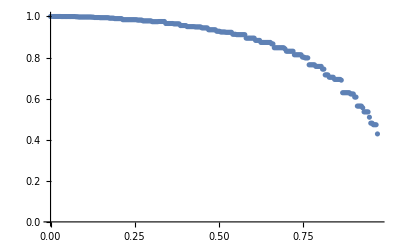

```mathematica
src=Import["I:/home/artem/projects/RhllTestOpt/build/trace/trace1d.txt", "Table"]//Flatten
data=Table[{(1  i)/Length[src],src[[i]]/src[[1]]},{i,1,Length[src]-7}];
data[[1,1]] = 0;
ListPlot[data]
```

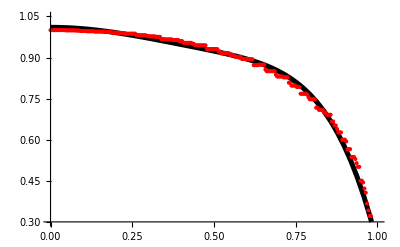

```mathematica
Parabola=Fit[data,{1,x^2,x^4,x^6},x];
Show[Plot[Parabola,{x,0,1},PlotStyle->Directive[Black, Thickness[0.009]],PlotRange->{{0,1},{0.3,1.05}}],
ListPlot[data,PlotStyle->Red]]
```

```mathematica
F={1,1.25,1.45,1.64,1.83,2.01,2.19,2.37,2.55,2.73,2.91}; (*c 119*)
f0=Table[{i*0.1,F[[i+1]]},{i,0,Length[F]-1}];
f=Interpolation [f0,InterpolationOrder->2];

ϕ2=Table[{√(1-(i/10)^2),f[i*0.1]/f[1]},{i,0,10}];
```

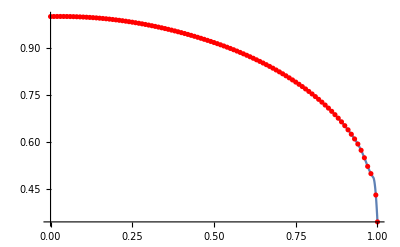

```mathematica
f2=Interpolation [ϕ2,InterpolationOrder->2, Method->"Spline"];
ϕ2=Table[{x,f2[x]},{x,0,1,0.01}];
ϕ2[[-1]] = {√(1-(0/10)^2),f[0*0.1]/f[1]};
ϕ2[[-2]] = {√(1-(1/10)^2),f[1*0.1]/f[1]};
Show[
Plot[f2[x],{x,0,1},PlotRange->All],
ListPlot[ϕ2,PlotStyle->Red]

]
```

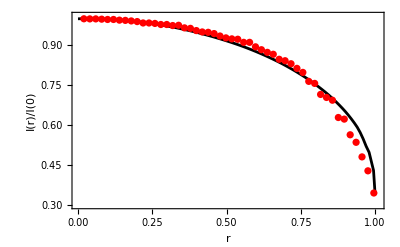

```mathematica
data2=Table[{(1  i)/Length[src],src[[i]]/src[[1]]},{i,5,Length[src]-1,5}];
Show[
ListPlot[ϕ2, Joined->True,PlotRange->{{0,1.01},{0.3,1.01}},
 PlotStyle->Directive[Black,Thickness[0.005]],
AxesStyle->Directive[Black, 14, Arrowheads[0.034]],
Frame->True,
FrameStyle->Directive[Black,14, Thickness[0.005]],
FrameLabel->{Style["r",16,FontFamily->"Times"],Style["I(r)/I(0)",16,FontFamily->"Times"]},
(*FrameLabel->{"Energy (keV)","EF(E) (Kev^2cm^-2s^-1keV^-1)"},*)
IntervalMarkersStyle->Directive[Black,Thickness[0.1]]

],
(*ListPlot[data2,PlotStyle->Directive[Red,Thickness[0.01]],Joined->True]*)
ListPlot[data2,PlotStyle->Directive[Red,PointSize[0.013]],Joined->False]

]
```

```mathematica
x=-Graphics-;
Export["Sphere.png",x]
```

Sphere.png

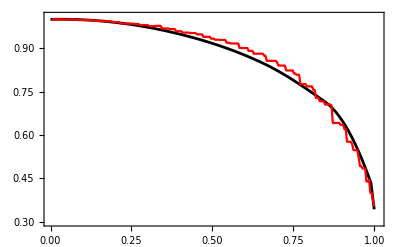

```mathematica
(*Tmp plots*)
src2=Import["I:/home/artem/projects/RhllTestOpt/build/trace/trace.txt", "Table"]//Flatten;
data3=Table[{(1  i)/Length[src2],src2[[i]]/src2[[1]]},{i,1,Length[src2]}];
Show[
ListPlot[ϕ2, Joined->True,
PlotRange->{{0,1.01},{0.3,1.01}},
 PlotStyle->Directive[Black,Thickness[0.005]],
AxesStyle->Directive[Black, 14, Arrowheads[0.034]],
Frame->True,
FrameStyle->Directive[Black,14, Thickness[0.005]],
(*FrameLabel->{"Energy (keV)","EF(E) (Kev^2cm^-2s^-1keV^-1)"},*)
IntervalMarkersStyle->Directive[Black,Thickness[0.1]]

],
ListPlot[data3,PlotStyle->Red,Joined->True]
]
```

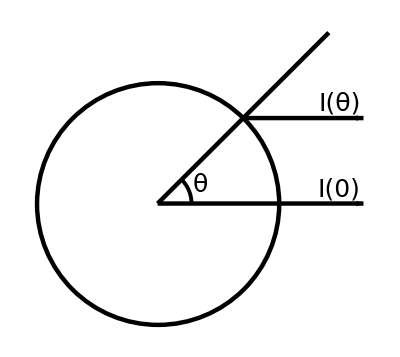

```mathematica
Show[
Graphics[{Thickness[0.008],Circle[{0,0},1],
Arrow[{{0,0},{1.7,0}}],
Line[{{0,0},{√2,√2}}],
Arrow[{{(√2)/2,(√2)/2},{1.7,(√2)/2}}]}],
Graphics[Text[Style["I(0)",25,FontFamily->"Times"],{1.5,0.12}]],
Graphics[Text[Style["I(θ)",25,FontFamily->"Times"],{1.5,(√2)/2+0.12}]],
Graphics[Text[Style["θ",25,FontFamily->"Times"],{0.35,0.15}]],
Graphics[{Thickness[0.007],Circle[{0,0},0.28,{0,Pi/4}]}]
]
```

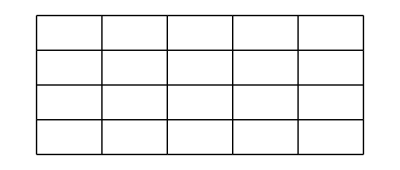

```mathematica
GraphicsGrid[Table[Table[,{j,1,5}],{i,1,4}],Frame->All]
```

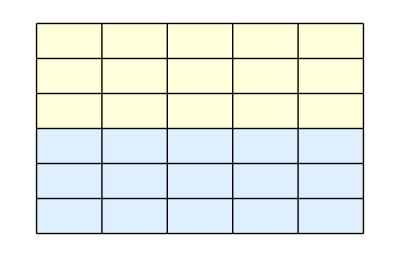

```mathematica
GraphicsGrid[Table[,{6},{5}],Dividers->{2->True,False},Background->{None,{{LightYellow,LightYellow,LightYellow,LightBlue,LightBlue,LightBlue}}},Frame->All]
```

```mathematica
GraphicsGrid[Table[Graphics[Circle[]],{6},{7}],Background->{None,{{LightBlue,LightBlue,LightBlue,Yellow,Yellow,Yellow}}},Frame->True];
```

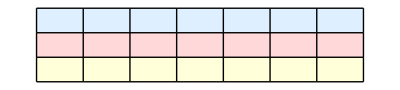

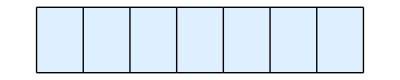

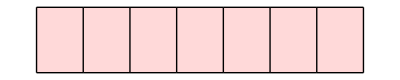

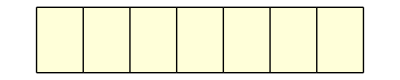

```mathematica
GraphicsGrid[Table[,{3},{7}],Background->{None,{{LightBlue,LightRed,LightYellow}}},Frame->All]
GraphicsGrid[Table[,{1},{7}],Background->{None,{{LightBlue}}},Frame->All]
GraphicsGrid[Table[,{1},{7}],Background->{None,{{LightRed}}},Frame->All]
GraphicsGrid[Table[,{1},{7}],Background->{None,{{LightYellow}}},Frame->All]
```

```mathematica
r=Graphics[{EdgeForm[Thick],White,Rectangle[]}];
```

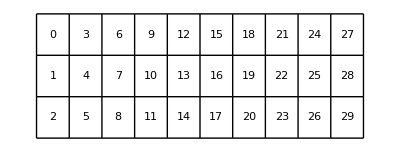

```mathematica
GraphicsGrid[Table[Text[Style[i+j*3,25,FontFamily->"Times"]],{i,0,2},{j,0,9}],Background->{None,{{White}}},Frame->All]
```

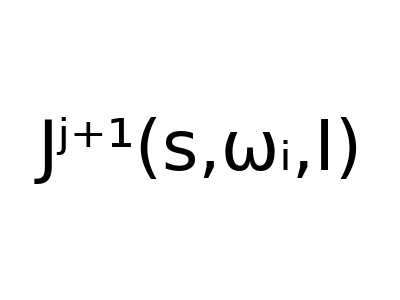

```mathematica
Graphics[Text[Style["J^(j+1)(s,ω_i,I)",70,FontFamily->"Times"]]]
```

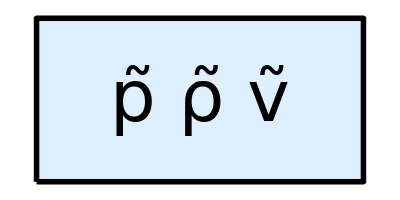

```mathematica
Show[
Graphics[{EdgeForm[Directive[Thickness[0.01],Black]],LightBlue,Rectangle[{2,1},{4,2}]}],
Graphics[Text[Style[ρ̃ ṽ p̃,90,FontFamily->"Times"],{3,1.5}]]
]
```

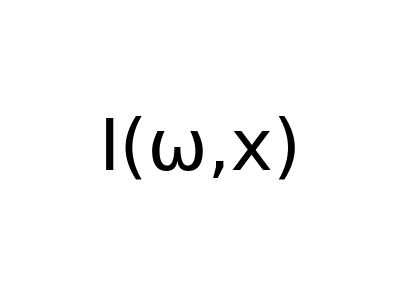

```mathematica
Graphics[Text[Style["I(ω,x)",150,FontFamily->"Times"]]]
```

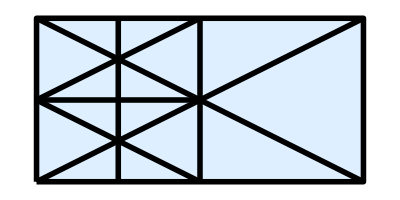

```mathematica
Show[
Graphics[{EdgeForm[Directive[Thickness[0.01],Black]],LightBlue,Rectangle[{2,1},{4,2}]}],
Graphics[{Directive[Thickness[0.01],Black],Line[{{2,1},{4,2}}],
Line[{{2,1.5},{3,2}}],
Line[{{2,1.5},{3,1}}],
Line[{{2,2},{4,1}}],
Line[{{2,1.5},{3,1.5}}],
Line[{{3,2},{3,1}}],
Line[{{2.5,2},{2.5,1}}]

}]
]
```

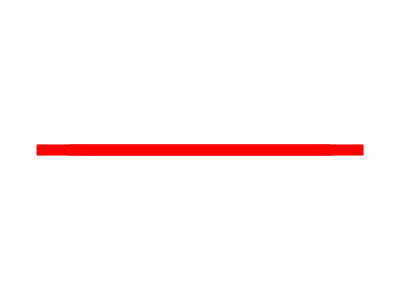

```mathematica
Graphics[{Directive[Thickness[0.02],Red],Arrowheads[0.2],Arrow[{{0.1,0},{1,0}}],Arrow[{{0.9,0},{0,0}}]}]
```